# Other Inverse Tangent Formulas

## Accompanies Section 1.4 of Experimental Mathematics: A Computational Perspective by Matthew P. Richey and Matthew L. Wright

## A sum of two arctangent values

We first consider the formula for π from equation (1.7) in the text:

π/4=arctan(1/2)+arctan(1/3)

Converting this formula to a series, we obtain equation (1.8) in the text:

We use a loop with an accumulator to add up partial sums of this series. We will put our code for this in a Module environment for convenient use later. Our module requires one parameter, m, the number of terms to add up.

```mathematica
piSum[m_]:=Module[
{acc=0}, (* initialize the accumulator as a local variable *)
Do[
acc+=(-1)^(n+1)(1/((2n-1)2^(2n-1))+1/((2n-1)3^(2n-1))), 
{n,1,m}];
4*acc  (* return value *)
]
```

Since we wrote our code using whole numbers and fractions, without any decimal points or use of the N function, Mathematica performs the computation using exact arithmetic. Thus, the module returns a fraction, which we can convert to a decimal. For example, here is the result with ten terms of the sum:

```mathematica
piSum[10]
N[piSum[10],20]
```

154739157603402615025/49255004804853399552

3.141592579606351211

Let’s compute many approximations. We’ll use the /@ shorthand for the Map function to compute a list of results.

```mathematica
maxTerms=10;
piValues=piSum/@Range[maxTerms]
```

{10/3,505/162,6115/1944,1538665/489888,498668825/158723712,21940173935/6983843328,10268124795235/3268438677504,1108954598674045/352991377170432,226226867530011415/72010240942768128,154739157603402615025/49255004804853399552}

Now we compute the accuracy of each approximation, using the log_10 method as in the text.

```mathematica
accuracy=N[-Log[10,Abs[Pi-piValues]],5]
```

{0.71729,1.6142,2.3997,3.1295,3.8281,4.5077,5.1747,5.8329,6.4845,7.1309}

We can print our findings in a table, similar to Table 1.5 in the text.

```mathematica
TableForm[Transpose[{Range[maxTerms],N[piValues,10],accuracy}],TableHeadings->{None,{"n","approx","accuracy"}}]
```

n | approx | accuracy
1 | 3.333333333 | 0.71729
2 | 3.117283951 | 1.6142
3 | 3.145576132 | 2.3997
4 | 3.140850562 | 3.1295
5 | 3.141741197 | 3.8281
6 | 3.141561588 | 4.5077
7 | 3.141599341 | 5.1747
8 | 3.141591184 | 5.8329
9 | 3.141592981 | 6.4845
10 | 3.14159258 | 7.1309

We can also display the accuracy values as a plot, similar to Figure 1.8 in the text.

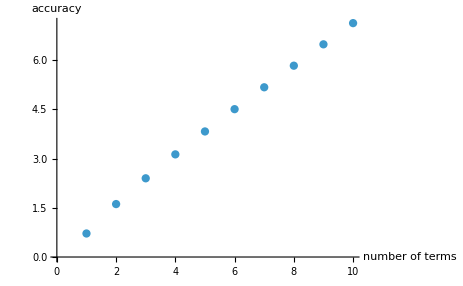

```mathematica
ListPlot[accuracy,AxesLabel->{"number of terms","accuracy"}]
```

The plot looks very nearly linear. Without any fancy line-fitting, we could simply compute the line through the first and last points of the plot. The slope and y-intercept of that line are as follows:

```mathematica
slope=(accuracy[[maxTerms]]-accuracy[[1]])/(maxTerms-1)
```

0.7126

```mathematica
intercept=accuracy[[1]]-slope
```

0.0047

We see that the slope is about 0.7, which means that each additional term of the sum increases the accuracy of the approximation of π by about 0.7 digits. To put it another way, each ten terms of the sum give us about seven more digits of π.

Now we will draw the previous plot together with the line through its first and last points.

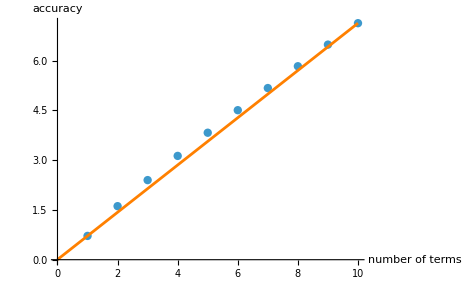

```mathematica
Show[
ListPlot[accuracy,AxesLabel->{"number of terms","accuracy"}],
Plot[slope*x+intercept,{x,0,maxTerms},PlotStyle->Orange]
]
```

If we want to find the line of best fit, we could use Mathematica’s LinearModelFit function.

```mathematica
linearModel=LinearModelFit[ Transpose[{Range[maxTerms],accuracy}], x, x]
```

FittedModel[…]

The slope of the linear model is close to what we computed earlier, though the intercept is not as close to zero as before.

Finally, we will plot our data points together with the line of best fit.

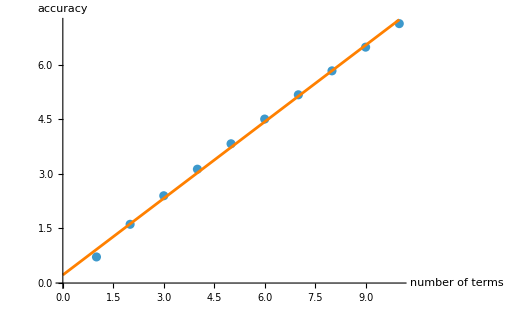

```mathematica
Show[
ListPlot[accuracy,AxesLabel->{"number of terms","accuracy"}],
Plot[linearModel[x],{x,0,maxTerms},PlotStyle->Orange]
]
```